# Supplementary tensors

```mathematica
SetDirectory[NotebookDirectory[]];
SetDirectory["../Rules"];
<<ITensor`
<<CTensor`
<<CITensor`
<<CIITensor`
<<CIIITensor`
<<CIIIITensor`
<<ETensor`
<<CETensor`
```

FeynCalc 9.3.1 (stable version). For help, use the documentation center, check out the wiki or visit the forum.

To save your and our time, please check our FAQ for answers to some common FeynCalc questions.

See also the supplied examples. If you use FeynCalc in your research, please cite

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 256 (2020) 107478, arXiv:2001.04407.

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 207 (2016) 432-444, arXiv:1601.01167.

• R. Mertig, M. Böhm, and A. Denner, Comput. Phys. Commun. 64 (1991) 345-359.

## ITensor

-Graphics-

The trimmed mean evaluation time is 0.00000874 seconds

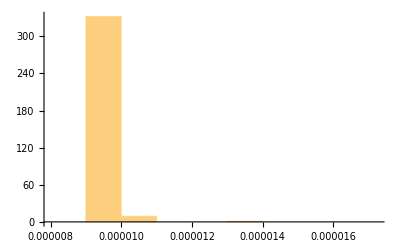

```mathematica
Table[Timing[ITensor[{}]][[1]],{n,500}];
Show[ListPlot[%,PlotMarkers->"x",AxesOrigin->{0,0},PlotRange->{{0,501},{0,1.2Max[%]}},PlotStyle->Black],Plot[{TrimmedMean[%,0.1],TrimmedMean[%,0.1]-StandardDeviation[%],TrimmedMean[%,0.1]+StandardDeviation[%]},{x,0,500},PlotStyle->{Black,Blue,Red},PlotLegends->{"TrimmedMean","TrimmedMean-StandardDeviation","TrimmedMean+StandardDeviation"}],ImageSize->Large]
Print["The trimmed mean evaluation time is "<>ToString[DecimalForm[TrimmedMean[%%,0.1]]]<>" seconds"]
Histogram[%%%]
```

-Graphics-

The trimmed mean evaluation time is 0.000025375 seconds

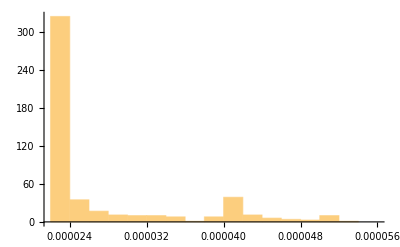

```mathematica
Table[Timing[ITensor[{r1,s1}]][[1]],{n,500}];
Show[ListPlot[%,PlotMarkers->"x",AxesOrigin->{0,0},PlotRange->{{0,501},{0,1.2Max[%]}},PlotStyle->Black],Plot[{TrimmedMean[%,0.1],TrimmedMean[%,0.1]-StandardDeviation[%],TrimmedMean[%,0.1]+StandardDeviation[%]},{x,0,500},PlotStyle->{Black,Blue,Red},PlotLegends->{"TrimmedMean","TrimmedMean-StandardDeviation","TrimmedMean+StandardDeviation"}],ImageSize->Large]
Print["The trimmed mean evaluation time is "<>ToString[TrimmedMean[%%,0.1]]<>" seconds"]
Histogram[%%%]
```

-Graphics-

The trimmed mean evaluation time is 0.000073995 seconds

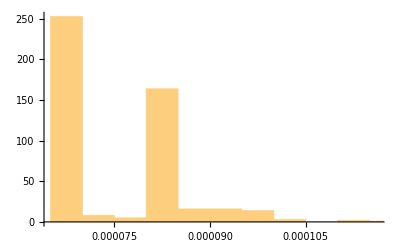

```mathematica
Table[Timing[ITensor[{r1,s1,r2,s2}]][[1]],{n,500}];
Show[ListPlot[%,PlotMarkers->"x",AxesOrigin->{0,0},PlotRange->{{0,501},{0,1.2Max[%]}},PlotStyle->Black],Plot[{TrimmedMean[%,0.1],TrimmedMean[%,0.1]-StandardDeviation[%],TrimmedMean[%,0.1]+StandardDeviation[%]},{x,0,500},PlotStyle->{Black,Blue,Red},PlotLegends->{"TrimmedMean","TrimmedMean-StandardDeviation","TrimmedMean+StandardDeviation"}],ImageSize->Large]
Print["The trimmed mean evaluation time is "<>ToString[TrimmedMean[%%,0.1]]<>" seconds"]
Histogram[%%%]
```

-Graphics-

The trimmed mean evaluation time is 0.000332705 seconds

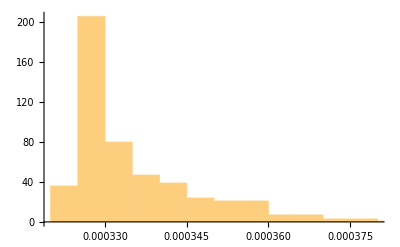

```mathematica
Table[Timing[ITensor[{r1,s1,r2,s2,r3,s3}]][[1]],{n,500}];
Show[ListPlot[%,PlotMarkers->"x",AxesOrigin->{0,0},PlotRange->{{0,501},{0,1.2Max[%]}},PlotStyle->Black],Plot[{TrimmedMean[%,0.1],TrimmedMean[%,0.1]-StandardDeviation[%],TrimmedMean[%,0.1]+StandardDeviation[%]},{x,0,500},PlotStyle->{Black,Blue,Red},PlotLegends->{"TrimmedMean","TrimmedMean-StandardDeviation","TrimmedMean+StandardDeviation"}],ImageSize->Large]
Print["The trimmed mean evaluation time is "<>ToString[TrimmedMean[%%,0.1]]<>" seconds"]
Histogram[%%%]
```

-Graphics-

The trimmed mean evaluation time is 0.00270384 seconds

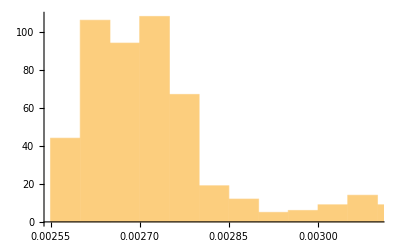

```mathematica
Table[Timing[ITensor[{r1,s1,r2,s2,r3,s3,r4,s4}]][[1]],{n,500}];
Show[ListPlot[%,PlotMarkers->"x",AxesOrigin->{0,0},PlotRange->{{0,501},{0,1.2Max[%]}},PlotStyle->Black],Plot[{TrimmedMean[%,0.1],TrimmedMean[%,0.1]-StandardDeviation[%],TrimmedMean[%,0.1]+StandardDeviation[%]},{x,0,500},PlotStyle->{Black,Blue,Red},PlotLegends->{"TrimmedMean","TrimmedMean-StandardDeviation","TrimmedMean+StandardDeviation"}],ImageSize->Large]
Print["The trimmed mean evaluation time is "<>ToString[TrimmedMean[%%,0.1]]<>" seconds"]
Histogram[%%%]
```

-Graphics-

The trimmed mean evaluation time is 0.0334726 seconds

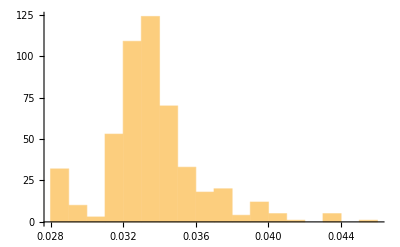

```mathematica
Table[Timing[ITensor[{r1,s1,r2,s2,r3,s3,r4,s4,r5,s5}]][[1]],{n,500}];
Show[ListPlot[%,PlotMarkers->"x",AxesOrigin->{0,0},PlotRange->{{0,501},{0,1.2Max[%]}},PlotStyle->Black],Plot[{TrimmedMean[%,0.1],TrimmedMean[%,0.1]-StandardDeviation[%],TrimmedMean[%,0.1]+StandardDeviation[%]},{x,0,500},PlotStyle->{Black,Blue,Red},PlotLegends->{"TrimmedMean","TrimmedMean-StandardDeviation","TrimmedMean+StandardDeviation"}],ImageSize->Large]
Print["The trimmed mean evaluation time is "<>ToString[TrimmedMean[%%,0.1]]<>" seconds"]
Histogram[%%%]
```

-Graphics-

The trimmed mean evaluation time is 1.45931 seconds

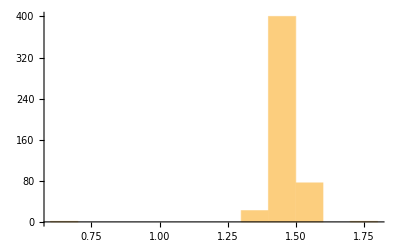

```mathematica
Table[Timing[ITensor[{r1,s1,r2,s2,r3,s3,r4,s4,r5,s5,r6,s6}]][[1]],{n,500}];
Show[ListPlot[%,PlotMarkers->"x",AxesOrigin->{0,0},PlotRange->{{0,501},{0,1.2Max[%]}},PlotStyle->Black],Plot[{TrimmedMean[%,0.1],TrimmedMean[%,0.1]-StandardDeviation[%],TrimmedMean[%,0.1]+StandardDeviation[%]},{x,0,500},PlotStyle->{Black,Blue,Red},PlotLegends->{"TrimmedMean","TrimmedMean-StandardDeviation","TrimmedMean+StandardDeviation"}],ImageSize->Large]
Print["The trimmed mean evaluation time is "<>ToString[TrimmedMean[%%,0.1]]<>" seconds"]
Histogram[%%%]
```

## CTensor

-Graphics-

The trimmed mean evaluation time is 0.000007755 seconds

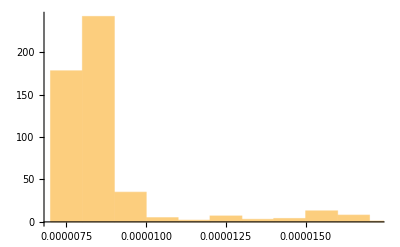

```mathematica
Table[Timing[CTensor[{}]][[1]],{n,500}];
Show[ListPlot[%,PlotMarkers->"x",AxesOrigin->{0,0},PlotRange->{{0,501},{0,1.2Max[%]}},PlotStyle->Black],Plot[{TrimmedMean[%,0.1],TrimmedMean[%,0.1]-StandardDeviation[%],TrimmedMean[%,0.1]+StandardDeviation[%]},{x,0,500},PlotStyle->{Black,Blue,Red},PlotLegends->{"TrimmedMean","TrimmedMean-StandardDeviation","TrimmedMean+StandardDeviation"}],ImageSize->Large]
Print["The trimmed mean evaluation time is "<>ToString[DecimalForm[TrimmedMean[%%,0.1]]]<>" seconds"]
Histogram[%%%]
```

-Graphics-

The trimmed mean evaluation time is 0.0000414725 seconds

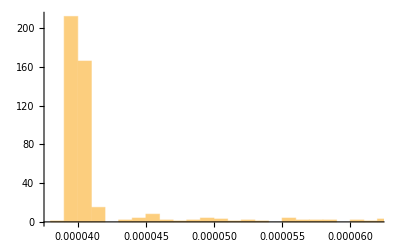

```mathematica
Table[Timing[CTensor[{r1,s1}]][[1]],{n,500}];
Show[ListPlot[%,PlotMarkers->"x",AxesOrigin->{0,0},PlotRange->{{0,501},{0,1.2Max[%]}},PlotStyle->Black],Plot[{TrimmedMean[%,0.1],TrimmedMean[%,0.1]-StandardDeviation[%],TrimmedMean[%,0.1]+StandardDeviation[%]},{x,0,500},PlotStyle->{Black,Blue,Red},PlotLegends->{"TrimmedMean","TrimmedMean-StandardDeviation","TrimmedMean+StandardDeviation"}],ImageSize->Large]
Print["The trimmed mean evaluation time is "<>ToString[TrimmedMean[%%,0.1]]<>" seconds"]
Histogram[%%%]
```

-Graphics-

The trimmed mean evaluation time is 0.000343923 seconds

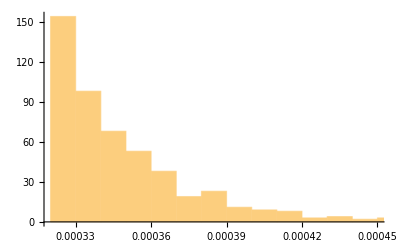

```mathematica
Table[Timing[CTensor[{r1,s1,r2,s2}]][[1]],{n,500}];
Show[ListPlot[%,PlotMarkers->"x",AxesOrigin->{0,0},PlotRange->{{0,501},{0,1.2Max[%]}},PlotStyle->Black],Plot[{TrimmedMean[%,0.1],TrimmedMean[%,0.1]-StandardDeviation[%],TrimmedMean[%,0.1]+StandardDeviation[%]},{x,0,500},PlotStyle->{Black,Blue,Red},PlotLegends->{"TrimmedMean","TrimmedMean-StandardDeviation","TrimmedMean+StandardDeviation"}],ImageSize->Large]
Print["The trimmed mean evaluation time is "<>ToString[TrimmedMean[%%,0.1]]<>" seconds"]
Histogram[%%%]
```

-Graphics-

The trimmed mean evaluation time is 0.00472434 seconds

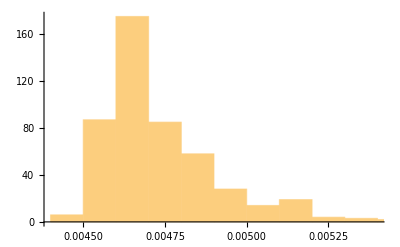

```mathematica
Table[Timing[CTensor[{r1,s1,r2,s2,r3,s3}]][[1]],{n,500}];
Show[ListPlot[%,PlotMarkers->"x",AxesOrigin->{0,0},PlotRange->{{0,501},{0,1.2Max[%]}},PlotStyle->Black],Plot[{TrimmedMean[%,0.1],TrimmedMean[%,0.1]-StandardDeviation[%],TrimmedMean[%,0.1]+StandardDeviation[%]},{x,0,500},PlotStyle->{Black,Blue,Red},PlotLegends->{"TrimmedMean","TrimmedMean-StandardDeviation","TrimmedMean+StandardDeviation"}],ImageSize->Large]
Print["The trimmed mean evaluation time is "<>ToString[TrimmedMean[%%,0.1]]<>" seconds"]
Histogram[%%%]
```

-Graphics-

The trimmed mean evaluation time is 0.092859 seconds

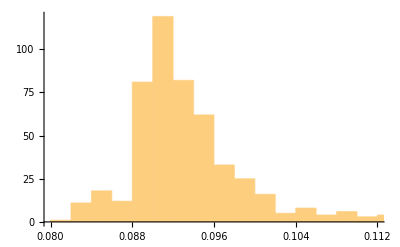

```mathematica
Table[Timing[CTensor[{r1,s1,r2,s2,r3,s3,r4,s4}]][[1]],{n,500}];
Show[ListPlot[%,PlotMarkers->"x",AxesOrigin->{0,0},PlotRange->{{0,501},{0,1.2Max[%]}},PlotStyle->Black],Plot[{TrimmedMean[%,0.1],TrimmedMean[%,0.1]-StandardDeviation[%],TrimmedMean[%,0.1]+StandardDeviation[%]},{x,0,500},PlotStyle->{Black,Blue,Red},PlotLegends->{"TrimmedMean","TrimmedMean-StandardDeviation","TrimmedMean+StandardDeviation"}],ImageSize->Large]
Print["The trimmed mean evaluation time is "<>ToString[TrimmedMean[%%,0.1]]<>" seconds"]
Histogram[%%%]
```

-Graphics-

The trimmed mean evaluation time is 2.21967 seconds

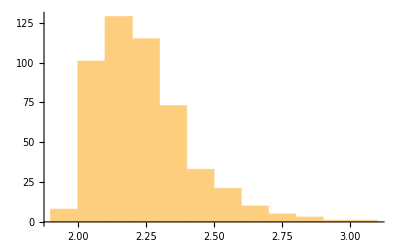

```mathematica
Table[Timing[CTensor[{r1,s1,r2,s2,r3,s3,r4,s4,r5,s5}]][[1]],{n,500}];
Show[ListPlot[%,PlotMarkers->"x",AxesOrigin->{0,0},PlotRange->{{0,501},{0,1.2Max[%]}},PlotStyle->Black],Plot[{TrimmedMean[%,0.1],TrimmedMean[%,0.1]-StandardDeviation[%],TrimmedMean[%,0.1]+StandardDeviation[%]},{x,0,500},PlotStyle->{Black,Blue,Red},PlotLegends->{"TrimmedMean","TrimmedMean-StandardDeviation","TrimmedMean+StandardDeviation"}],ImageSize->Large]
Print["The trimmed mean evaluation time is "<>ToString[TrimmedMean[%%,0.1]]<>" seconds"]
Histogram[%%%]
```

## CITensor

-Graphics-

The trimmed mean evaluation time is 0.0000239125 seconds

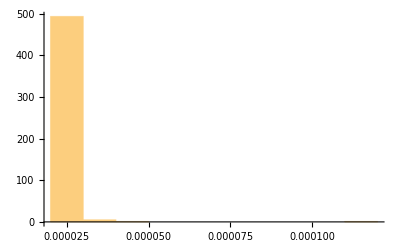

```mathematica
Table[Timing[CITensor[{μ,ν},{}]][[1]],{n,500}];
Show[ListPlot[%,PlotMarkers->"x",AxesOrigin->{0,0},PlotRange->{{0,501},{0,1.2Max[%]}},PlotStyle->Black],Plot[{TrimmedMean[%,0.1],TrimmedMean[%,0.1]-StandardDeviation[%],TrimmedMean[%,0.1]+StandardDeviation[%]},{x,0,500},PlotStyle->{Black,Blue,Red},PlotLegends->{"TrimmedMean","TrimmedMean-StandardDeviation","TrimmedMean+StandardDeviation"}],ImageSize->Large]
Print["The trimmed mean evaluation time is "<>ToString[TrimmedMean[%%,0.1]]<>" seconds"]
Histogram[%%%]
```

-Graphics-

The trimmed mean evaluation time is 0.00008629 seconds

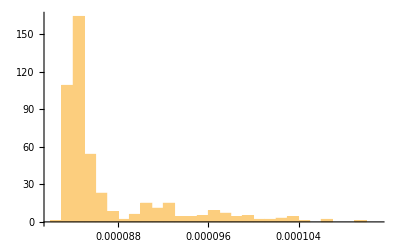

```mathematica
Table[Timing[CITensor[{μ,ν},{r1,s1}]][[1]],{n,500}];
Show[ListPlot[%,PlotMarkers->"x",AxesOrigin->{0,0},PlotRange->{{0,501},{0,1.2Max[%]}},PlotStyle->Black],Plot[{TrimmedMean[%,0.1],TrimmedMean[%,0.1]-StandardDeviation[%],TrimmedMean[%,0.1]+StandardDeviation[%]},{x,0,500},PlotStyle->{Black,Blue,Red},PlotLegends->{"TrimmedMean","TrimmedMean-StandardDeviation","TrimmedMean+StandardDeviation"}],ImageSize->Large]
Print["The trimmed mean evaluation time is "<>ToString[TrimmedMean[%%,0.1]]<>" seconds"]
Histogram[%%%]
```

-Graphics-

The trimmed mean evaluation time is 0.000775557 seconds

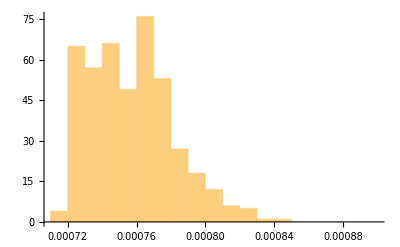

```mathematica
Table[Timing[CITensor[{μ,ν},{r1,s1,r2,s2}]][[1]],{n,500}];
Show[ListPlot[%,PlotMarkers->"x",AxesOrigin->{0,0},PlotRange->{{0,501},{0,1.2Max[%]}},PlotStyle->Black],Plot[{TrimmedMean[%,0.1],TrimmedMean[%,0.1]-StandardDeviation[%],TrimmedMean[%,0.1]+StandardDeviation[%]},{x,0,500},PlotStyle->{Black,Blue,Red},PlotLegends->{"TrimmedMean","TrimmedMean-StandardDeviation","TrimmedMean+StandardDeviation"}],ImageSize->Large]
Print["The trimmed mean evaluation time is "<>ToString[TrimmedMean[%%,0.1]]<>" seconds"]
Histogram[%%%]
```

-Graphics-

The trimmed mean evaluation time is 0.0109196 seconds

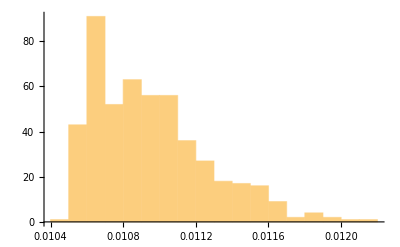

```mathematica
Table[Timing[CITensor[{μ,ν},{r1,s1,r2,s2,r3,s3}]][[1]],{n,500}];
Show[ListPlot[%,PlotMarkers->"x",AxesOrigin->{0,0},PlotRange->{{0,501},{0,1.2Max[%]}},PlotStyle->Black],Plot[{TrimmedMean[%,0.1],TrimmedMean[%,0.1]-StandardDeviation[%],TrimmedMean[%,0.1]+StandardDeviation[%]},{x,0,500},PlotStyle->{Black,Blue,Red},PlotLegends->{"TrimmedMean","TrimmedMean-StandardDeviation","TrimmedMean+StandardDeviation"}],ImageSize->Large]
Print["The trimmed mean evaluation time is "<>ToString[TrimmedMean[%%,0.1]]<>" seconds"]
Histogram[%%%]
```

-Graphics-

The trimmed mean evaluation time is 0.216967 seconds

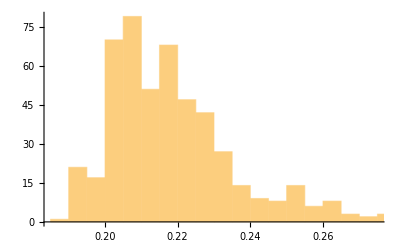

```mathematica
Table[Timing[CITensor[{μ,ν},{r1,s1,r2,s2,r3,s3,r5,s5}]][[1]],{n,500}];
Show[ListPlot[%,PlotMarkers->"x",AxesOrigin->{0,0},PlotRange->{{0,501},{0,1.2Max[%]}},PlotStyle->Black],Plot[{TrimmedMean[%,0.1],TrimmedMean[%,0.1]-StandardDeviation[%],TrimmedMean[%,0.1]+StandardDeviation[%]},{x,0,500},PlotStyle->{Black,Blue,Red},PlotLegends->{"TrimmedMean","TrimmedMean-StandardDeviation","TrimmedMean+StandardDeviation"}],ImageSize->Large]
Print["The trimmed mean evaluation time is "<>ToString[TrimmedMean[%%,0.1]]<>" seconds"]
Histogram[%%%]
```

-Graphics-

The trimmed mean evaluation time is 5.90179 seconds

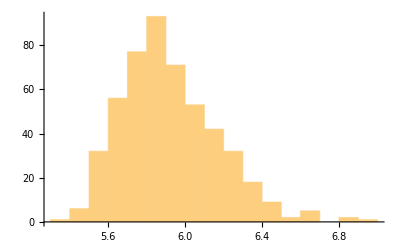

```mathematica
Table[Timing[CITensor[{μ,ν},{r1,s1,r2,s2,r3,s3,r5,s5,r6,s6}]][[1]],{n,500}];
Show[ListPlot[%,PlotMarkers->"x",AxesOrigin->{0,0},PlotRange->{{0,501},{0,1.2Max[%]}},PlotStyle->Black],Plot[{TrimmedMean[%,0.1],TrimmedMean[%,0.1]-StandardDeviation[%],TrimmedMean[%,0.1]+StandardDeviation[%]},{x,0,500},PlotStyle->{Black,Blue,Red},PlotLegends->{"TrimmedMean","TrimmedMean-StandardDeviation","TrimmedMean+StandardDeviation"}],ImageSize->Large]
Print["The trimmed mean evaluation time is "<>ToString[TrimmedMean[%%,0.1]]<>" seconds"]
Histogram[%%%]
```

## CIITensor

-Graphics-

The trimmed mean evaluation time is 0.000063475 seconds

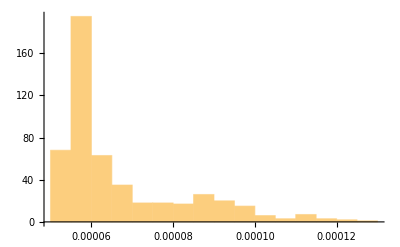

```mathematica
Table[Timing[CIITensor[{μ,ν,α,β},{}]][[1]],{n,500}];
Show[ListPlot[%,PlotMarkers->"x",AxesOrigin->{0,0},PlotRange->{{0,501},{0,1.2Max[%]}},PlotStyle->Black],Plot[{TrimmedMean[%,0.1],TrimmedMean[%,0.1]-StandardDeviation[%],TrimmedMean[%,0.1]+StandardDeviation[%]},{x,0,500},PlotStyle->{Black,Blue,Red},PlotLegends->{"TrimmedMean","TrimmedMean-StandardDeviation","TrimmedMean+StandardDeviation"}],ImageSize->Large]
Print["The trimmed mean evaluation time is "<>ToString[TrimmedMean[%%,0.1]]<>" seconds"]
Histogram[%%%]
```

-Graphics-

The trimmed mean evaluation time is 0.000357945 seconds

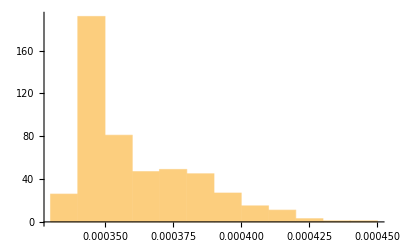

```mathematica
Table[Timing[CIITensor[{μ,ν,α,β},{r1,s1}]][[1]],{n,500}];
Show[ListPlot[%,PlotMarkers->"x",AxesOrigin->{0,0},PlotRange->{{0,501},{0,1.2Max[%]}},PlotStyle->Black],Plot[{TrimmedMean[%,0.1],TrimmedMean[%,0.1]-StandardDeviation[%],TrimmedMean[%,0.1]+StandardDeviation[%]},{x,0,500},PlotStyle->{Black,Blue,Red},PlotLegends->{"TrimmedMean","TrimmedMean-StandardDeviation","TrimmedMean+StandardDeviation"}],ImageSize->Large]
Print["The trimmed mean evaluation time is "<>ToString[TrimmedMean[%%,0.1]]<>" seconds"]
Histogram[%%%]
```

-Graphics-

The trimmed mean evaluation time is 0.00322368 seconds

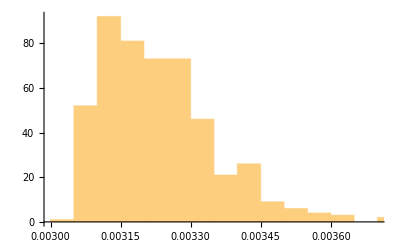

```mathematica
Table[Timing[CIITensor[{μ,ν,α,β},{r1,s1,r2,s2}]][[1]],{n,500}];
Show[ListPlot[%,PlotMarkers->"x",AxesOrigin->{0,0},PlotRange->{{0,501},{0,1.2Max[%]}},PlotStyle->Black],Plot[{TrimmedMean[%,0.1],TrimmedMean[%,0.1]-StandardDeviation[%],TrimmedMean[%,0.1]+StandardDeviation[%]},{x,0,500},PlotStyle->{Black,Blue,Red},PlotLegends->{"TrimmedMean","TrimmedMean-StandardDeviation","TrimmedMean+StandardDeviation"}],ImageSize->Large]
Print["The trimmed mean evaluation time is "<>ToString[TrimmedMean[%%,0.1]]<>" seconds"]
Histogram[%%%]
```

-Graphics-

The trimmed mean evaluation time is 0.0448911 seconds

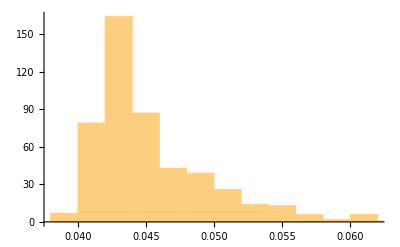

```mathematica
Table[Timing[CIITensor[{μ,ν,α,β},{r1,s1,r2,s2,r3,s3}]][[1]],{n,500}];
Show[ListPlot[%,PlotMarkers->"x",AxesOrigin->{0,0},PlotRange->{{0,501},{0,1.2Max[%]}},PlotStyle->Black],Plot[{TrimmedMean[%,0.1],TrimmedMean[%,0.1]-StandardDeviation[%],TrimmedMean[%,0.1]+StandardDeviation[%]},{x,0,500},PlotStyle->{Black,Blue,Red},PlotLegends->{"TrimmedMean","TrimmedMean-StandardDeviation","TrimmedMean+StandardDeviation"}],ImageSize->Large]
Print["The trimmed mean evaluation time is "<>ToString[TrimmedMean[%%,0.1]]<>" seconds"]
Histogram[%%%]
```

-Graphics-

The trimmed mean evaluation time is 1.72978 seconds

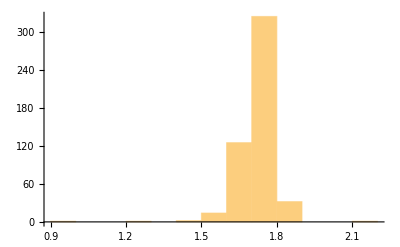

```mathematica
Table[Timing[CIITensor[{μ,ν,α,β},{r1,s1,r2,s2,r3,s3,r4,s4}]][[1]],{n,500}];
Show[ListPlot[%,PlotMarkers->"x",AxesOrigin->{0,0},PlotRange->{{0,501},{0,1.2Max[%]}},PlotStyle->Black],Plot[{TrimmedMean[%,0.1],TrimmedMean[%,0.1]-StandardDeviation[%],TrimmedMean[%,0.1]+StandardDeviation[%]},{x,0,500},PlotStyle->{Black,Blue,Red},PlotLegends->{"TrimmedMean","TrimmedMean-StandardDeviation","TrimmedMean+StandardDeviation"}],ImageSize->Large]
Print["The trimmed mean evaluation time is "<>ToString[TrimmedMean[%%,0.1]]<>" seconds"]
Histogram[%%%]
```

## CIIITensor

-Graphics-

The trimmed mean evaluation time is 0.000123073 seconds

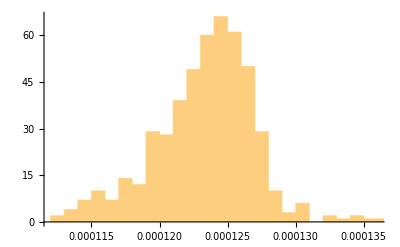

```mathematica
Table[Timing[CIIITensor[{μ,ν,α,β,ρ,σ},{}]][[1]],{n,500}];
Show[ListPlot[%,PlotMarkers->"x",AxesOrigin->{0,0},PlotRange->{{0,501},{0,1.2Max[%]}},PlotStyle->Black],Plot[{TrimmedMean[%,0.1],TrimmedMean[%,0.1]-StandardDeviation[%],TrimmedMean[%,0.1]+StandardDeviation[%]},{x,0,500},PlotStyle->{Black,Blue,Red},PlotLegends->{"TrimmedMean","TrimmedMean-StandardDeviation","TrimmedMean+StandardDeviation"}],ImageSize->Large]
Print["The trimmed mean evaluation time is "<>ToString[TrimmedMean[%%,0.1]]<>" seconds"]
Histogram[%%%]
```

-Graphics-

The trimmed mean evaluation time is 0.00052459 seconds

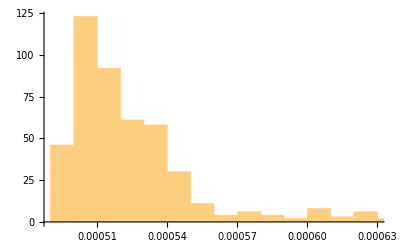

```mathematica
Table[Timing[CIIITensor[{μ,ν,α,β,ρ,σ},{r1,s1}]][[1]],{n,500}];
Show[ListPlot[%,PlotMarkers->"x",AxesOrigin->{0,0},PlotRange->{{0,501},{0,1.2Max[%]}},PlotStyle->Black],Plot[{TrimmedMean[%,0.1],TrimmedMean[%,0.1]-StandardDeviation[%],TrimmedMean[%,0.1]+StandardDeviation[%]},{x,0,500},PlotStyle->{Black,Blue,Red},PlotLegends->{"TrimmedMean","TrimmedMean-StandardDeviation","TrimmedMean+StandardDeviation"}],ImageSize->Large]
Print["The trimmed mean evaluation time is "<>ToString[TrimmedMean[%%,0.1]]<>" seconds"]
Histogram[%%%]
```

-Graphics-

The trimmed mean evaluation time is 0.00634697 seconds

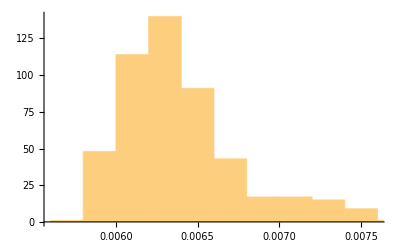

```mathematica
Table[Timing[CIIITensor[{μ,ν,α,β,ρ,σ},{r1,s1,r2,s2}]][[1]],{n,500}];
Show[ListPlot[%,PlotMarkers->"x",AxesOrigin->{0,0},PlotRange->{{0,501},{0,1.2Max[%]}},PlotStyle->Black],Plot[{TrimmedMean[%,0.1],TrimmedMean[%,0.1]-StandardDeviation[%],TrimmedMean[%,0.1]+StandardDeviation[%]},{x,0,500},PlotStyle->{Black,Blue,Red},PlotLegends->{"TrimmedMean","TrimmedMean-StandardDeviation","TrimmedMean+StandardDeviation"}],ImageSize->Large]
Print["The trimmed mean evaluation time is "<>ToString[TrimmedMean[%%,0.1]]<>" seconds"]
Histogram[%%%]
```

-Graphics-

The trimmed mean evaluation time is 0.101317 seconds

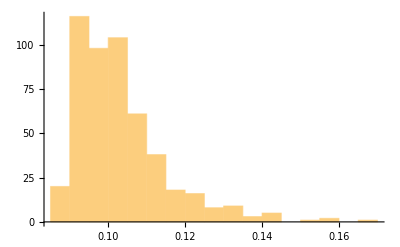

```mathematica
Table[Timing[CIIITensor[{μ,ν,α,β,ρ,σ},{r1,s1,r2,s2,r3,s3}]][[1]],{n,500}];
Show[ListPlot[%,PlotMarkers->"x",AxesOrigin->{0,0},PlotRange->{{0,501},{0,1.2Max[%]}},PlotStyle->Black],Plot[{TrimmedMean[%,0.1],TrimmedMean[%,0.1]-StandardDeviation[%],TrimmedMean[%,0.1]+StandardDeviation[%]},{x,0,500},PlotStyle->{Black,Blue,Red},PlotLegends->{"TrimmedMean","TrimmedMean-StandardDeviation","TrimmedMean+StandardDeviation"}],ImageSize->Large]
Print["The trimmed mean evaluation time is "<>ToString[TrimmedMean[%%,0.1]]<>" seconds"]
Histogram[%%%]
```

-Graphics-

The trimmed mean evaluation time is 2.66493 seconds

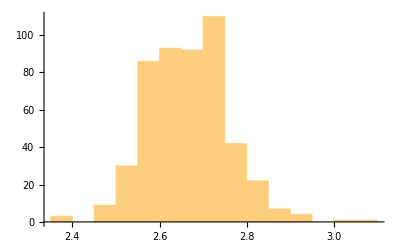

```mathematica
Table[Timing[CIIITensor[{μ,ν,α,β,ρ,σ},{r1,s1,r2,s2,r3,s3,r4,s4}]][[1]],{n,500}];
Show[ListPlot[%,PlotMarkers->"x",AxesOrigin->{0,0},PlotRange->{{0,501},{0,1.2Max[%]}},PlotStyle->Black],Plot[{TrimmedMean[%,0.1],TrimmedMean[%,0.1]-StandardDeviation[%],TrimmedMean[%,0.1]+StandardDeviation[%]},{x,0,500},PlotStyle->{Black,Blue,Red},PlotLegends->{"TrimmedMean","TrimmedMean-StandardDeviation","TrimmedMean+StandardDeviation"}],ImageSize->Large]
Print["The trimmed mean evaluation time is "<>ToString[TrimmedMean[%%,0.1]]<>" seconds"]
Histogram[%%%]
```

## CIIIITensor

-Graphics-

The trimmed mean evaluation time is 0.000109908 seconds

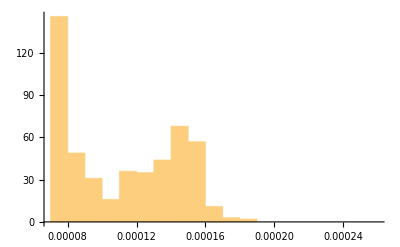

```mathematica
Table[Timing[CIIIITensor[{μ,ν,α,β,ρ,σ},{}]][[1]],{n,500}];
Show[ListPlot[%,PlotMarkers->"x",AxesOrigin->{0,0},PlotRange->{{0,501},{0,1.2Max[%]}},PlotStyle->Black],Plot[{TrimmedMean[%,0.1],TrimmedMean[%,0.1]-StandardDeviation[%],TrimmedMean[%,0.1]+StandardDeviation[%]},{x,0,500},PlotStyle->{Black,Blue,Red},PlotLegends->{"TrimmedMean","TrimmedMean-StandardDeviation","TrimmedMean+StandardDeviation"}],ImageSize->Large]
Print["The trimmed mean evaluation time is "<>ToString[TrimmedMean[%%,0.1]]<>" seconds"]
Histogram[%%%]
```

-Graphics-

The trimmed mean evaluation time is 0.000661518 seconds

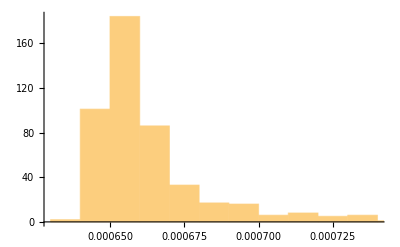

```mathematica
Table[Timing[CIIIITensor[{μ,ν,α,β,ρ,σ},{r1,s1}]][[1]],{n,500}];
Show[ListPlot[%,PlotMarkers->"x",AxesOrigin->{0,0},PlotRange->{{0,501},{0,1.2Max[%]}},PlotStyle->Black],Plot[{TrimmedMean[%,0.1],TrimmedMean[%,0.1]-StandardDeviation[%],TrimmedMean[%,0.1]+StandardDeviation[%]},{x,0,500},PlotStyle->{Black,Blue,Red},PlotLegends->{"TrimmedMean","TrimmedMean-StandardDeviation","TrimmedMean+StandardDeviation"}],ImageSize->Large]
Print["The trimmed mean evaluation time is "<>ToString[TrimmedMean[%%,0.1]]<>" seconds"]
Histogram[%%%]
```

-Graphics-

The trimmed mean evaluation time is 0.0102097 seconds

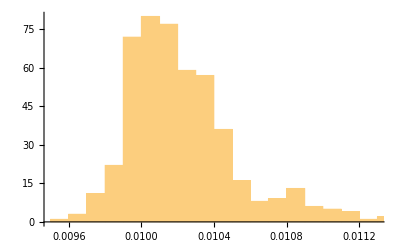

```mathematica
Table[Timing[CIIIITensor[{μ,ν,α,β,ρ,σ},{r1,s1,r2,s2}]][[1]],{n,500}];
Show[ListPlot[%,PlotMarkers->"x",AxesOrigin->{0,0},PlotRange->{{0,501},{0,1.2Max[%]}},PlotStyle->Black],Plot[{TrimmedMean[%,0.1],TrimmedMean[%,0.1]-StandardDeviation[%],TrimmedMean[%,0.1]+StandardDeviation[%]},{x,0,500},PlotStyle->{Black,Blue,Red},PlotLegends->{"TrimmedMean","TrimmedMean-StandardDeviation","TrimmedMean+StandardDeviation"}],ImageSize->Large]
Print["The trimmed mean evaluation time is "<>ToString[TrimmedMean[%%,0.1]]<>" seconds"]
Histogram[%%%]
```

-Graphics-

The trimmed mean evaluation time is 0.189404 seconds

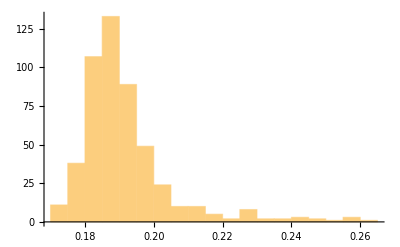

```mathematica
Table[Timing[CIIIITensor[{μ,ν,α,β,ρ,σ},{r1,s1,r2,s2,r3,s3}]][[1]],{n,500}];
Show[ListPlot[%,PlotMarkers->"x",AxesOrigin->{0,0},PlotRange->{{0,501},{0,1.2Max[%]}},PlotStyle->Black],Plot[{TrimmedMean[%,0.1],TrimmedMean[%,0.1]-StandardDeviation[%],TrimmedMean[%,0.1]+StandardDeviation[%]},{x,0,500},PlotStyle->{Black,Blue,Red},PlotLegends->{"TrimmedMean","TrimmedMean-StandardDeviation","TrimmedMean+StandardDeviation"}],ImageSize->Large]
Print["The trimmed mean evaluation time is "<>ToString[TrimmedMean[%%,0.1]]<>" seconds"]
Histogram[%%%]
```

-Graphics-

The trimmed mean evaluation time is 5.00713 seconds

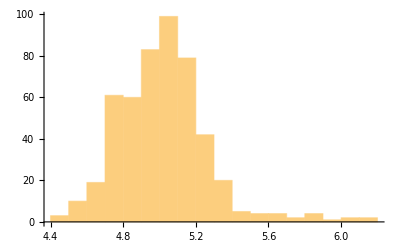

```mathematica
Table[Timing[CIIIITensor[{μ,ν,α,β,ρ,σ},{r1,s1,r2,s2,r3,s3,r4,s4}]][[1]],{n,500}];
Show[ListPlot[%,PlotMarkers->"x",AxesOrigin->{0,0},PlotRange->{{0,501},{0,1.2Max[%]}},PlotStyle->Black],Plot[{TrimmedMean[%,0.1],TrimmedMean[%,0.1]-StandardDeviation[%],TrimmedMean[%,0.1]+StandardDeviation[%]},{x,0,500},PlotStyle->{Black,Blue,Red},PlotLegends->{"TrimmedMean","TrimmedMean-StandardDeviation","TrimmedMean+StandardDeviation"}],ImageSize->Large]
Print["The trimmed mean evaluation time is "<>ToString[TrimmedMean[%%,0.1]]<>" seconds"]
Histogram[%%%]
```

## ETensor

-Graphics-

The trimmed mean evaluation time is 0.0000123475 seconds

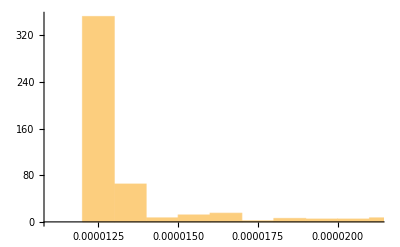

```mathematica
Table[Timing[ETensor[{μ,ν},{}]][[1]],{n,500}];
Show[ListPlot[%,PlotMarkers->"x",AxesOrigin->{0,0},PlotRange->{{0,501},{0,1.2Max[%]}},PlotStyle->Black],Plot[{TrimmedMean[%,0.1],TrimmedMean[%,0.1]-StandardDeviation[%],TrimmedMean[%,0.1]+StandardDeviation[%]},{x,0,500},PlotStyle->{Black,Blue,Red},PlotLegends->{"TrimmedMean","TrimmedMean-StandardDeviation","TrimmedMean+StandardDeviation"}],ImageSize->Large]
Print["The trimmed mean evaluation time is "<>ToString[DecimalForm[TrimmedMean[%%,0.1]]]<>" seconds"]
Histogram[%%%]
```

-Graphics-

The trimmed mean evaluation time is 0.0000353375 seconds

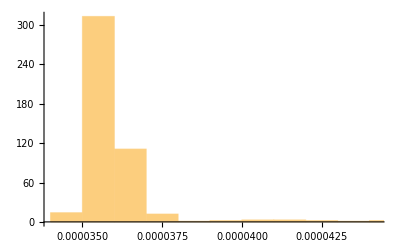

```mathematica
Table[Timing[ETensor[{μ,ν},{r1,s1}]][[1]],{n,500}];
Show[ListPlot[%,PlotMarkers->"x",AxesOrigin->{0,0},PlotRange->{{0,501},{0,1.2Max[%]}},PlotStyle->Black],Plot[{TrimmedMean[%,0.1],TrimmedMean[%,0.1]-StandardDeviation[%],TrimmedMean[%,0.1]+StandardDeviation[%]},{x,0,500},PlotStyle->{Black,Blue,Red},PlotLegends->{"TrimmedMean","TrimmedMean-StandardDeviation","TrimmedMean+StandardDeviation"}],ImageSize->Large]
Print["The trimmed mean evaluation time is "<>ToString[DecimalForm[TrimmedMean[%%,0.1]]]<>" seconds"]
Histogram[%%%]
```

-Graphics-

The trimmed mean evaluation time is 0.000121123 seconds

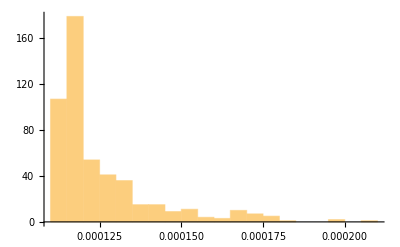

```mathematica
Table[Timing[ETensor[{μ,ν},{r1,s1,r2,s2}]][[1]],{n,500}];
Show[ListPlot[%,PlotMarkers->"x",AxesOrigin->{0,0},PlotRange->{{0,501},{0,1.2Max[%]}},PlotStyle->Black],Plot[{TrimmedMean[%,0.1],TrimmedMean[%,0.1]-StandardDeviation[%],TrimmedMean[%,0.1]+StandardDeviation[%]},{x,0,500},PlotStyle->{Black,Blue,Red},PlotLegends->{"TrimmedMean","TrimmedMean-StandardDeviation","TrimmedMean+StandardDeviation"}],ImageSize->Large]
Print["The trimmed mean evaluation time is "<>ToString[DecimalForm[TrimmedMean[%%,0.1]]]<>" seconds"]
Histogram[%%%]
```

-Graphics-

The trimmed mean evaluation time is 0.00065242 seconds

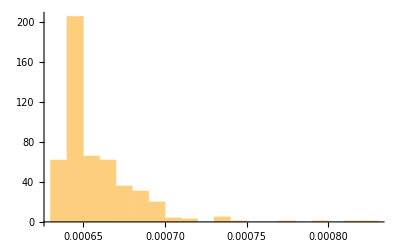

```mathematica
Table[Timing[ETensor[{μ,ν},{r1,s1,r2,s2,r3,s3}]][[1]],{n,500}];
Show[ListPlot[%,PlotMarkers->"x",AxesOrigin->{0,0},PlotRange->{{0,501},{0,1.2Max[%]}},PlotStyle->Black],Plot[{TrimmedMean[%,0.1],TrimmedMean[%,0.1]-StandardDeviation[%],TrimmedMean[%,0.1]+StandardDeviation[%]},{x,0,500},PlotStyle->{Black,Blue,Red},PlotLegends->{"TrimmedMean","TrimmedMean-StandardDeviation","TrimmedMean+StandardDeviation"}],ImageSize->Large]
Print["The trimmed mean evaluation time is "<>ToString[DecimalForm[TrimmedMean[%%,0.1]]]<>" seconds"]
Histogram[%%%]
```

-Graphics-

The trimmed mean evaluation time is 0.00551733 seconds

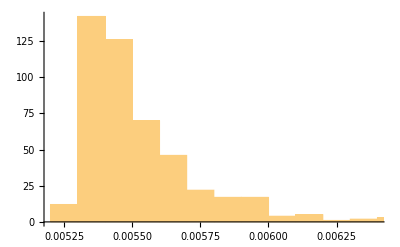

```mathematica
Table[Timing[ETensor[{μ,ν},{r1,s1,r2,s2,r3,s3,r4,s4}]][[1]],{n,500}];
Show[ListPlot[%,PlotMarkers->"x",AxesOrigin->{0,0},PlotRange->{{0,501},{0,1.2Max[%]}},PlotStyle->Black],Plot[{TrimmedMean[%,0.1],TrimmedMean[%,0.1]-StandardDeviation[%],TrimmedMean[%,0.1]+StandardDeviation[%]},{x,0,500},PlotStyle->{Black,Blue,Red},PlotLegends->{"TrimmedMean","TrimmedMean-StandardDeviation","TrimmedMean+StandardDeviation"}],ImageSize->Large]
Print["The trimmed mean evaluation time is "<>ToString[DecimalForm[TrimmedMean[%%,0.1]]]<>" seconds"]
Histogram[%%%]
```

-Graphics-

The trimmed mean evaluation time is 0.0642345 seconds

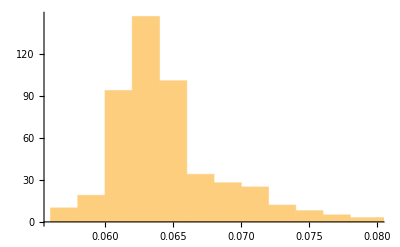

```mathematica
Table[Timing[ETensor[{μ,ν},{r1,s1,r2,s2,r3,s3,r4,s4,r5,s5}]][[1]],{n,500}];
Show[ListPlot[%,PlotMarkers->"x",AxesOrigin->{0,0},PlotRange->{{0,501},{0,1.2Max[%]}},PlotStyle->Black],Plot[{TrimmedMean[%,0.1],TrimmedMean[%,0.1]-StandardDeviation[%],TrimmedMean[%,0.1]+StandardDeviation[%]},{x,0,500},PlotStyle->{Black,Blue,Red},PlotLegends->{"TrimmedMean","TrimmedMean-StandardDeviation","TrimmedMean+StandardDeviation"}],ImageSize->Large]
Print["The trimmed mean evaluation time is "<>ToString[DecimalForm[TrimmedMean[%%,0.1]]]<>" seconds"]
Histogram[%%%]
```

-Graphics-

The trimmed mean evaluation time is 0.947963 seconds

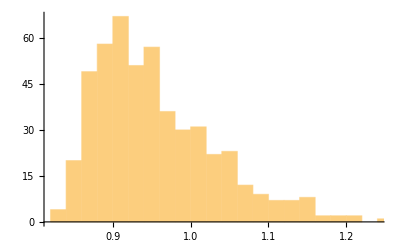

```mathematica
Table[Timing[ETensor[{μ,ν},{r1,s1,r2,s2,r3,s3,r4,s4,r5,s5,r6,s6}]][[1]],{n,500}];
Show[ListPlot[%,PlotMarkers->"x",AxesOrigin->{0,0},PlotRange->{{0,501},{0,1.2Max[%]}},PlotStyle->Black],Plot[{TrimmedMean[%,0.1],TrimmedMean[%,0.1]-StandardDeviation[%],TrimmedMean[%,0.1]+StandardDeviation[%]},{x,0,500},PlotStyle->{Black,Blue,Red},PlotLegends->{"TrimmedMean","TrimmedMean-StandardDeviation","TrimmedMean+StandardDeviation"}],ImageSize->Large]
Print["The trimmed mean evaluation time is "<>ToString[DecimalForm[TrimmedMean[%%,0.1]]]<>" seconds"]
Histogram[%%%]
```

## CETensor

-Graphics-

The trimmed mean evaluation time is 0.0000229325 seconds

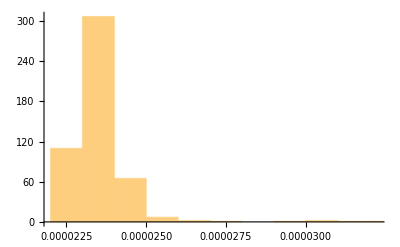

```mathematica
Table[Timing[ETensor[{μ,ν},{}]][[1]],{n,500}];
Show[ListPlot[%,PlotMarkers->"x",AxesOrigin->{0,0},PlotRange->{{0,501},{0,1.2Max[%]}},PlotStyle->Black],Plot[{TrimmedMean[%,0.1],TrimmedMean[%,0.1]-StandardDeviation[%],TrimmedMean[%,0.1]+StandardDeviation[%]},{x,0,500},PlotStyle->{Black,Blue,Red},PlotLegends->{"TrimmedMean","TrimmedMean-StandardDeviation","TrimmedMean+StandardDeviation"}],ImageSize->Large]
Print["The trimmed mean evaluation time is "<>ToString[DecimalForm[TrimmedMean[%%,0.1]]]<>" seconds"]
Histogram[%%%]
```

-Graphics-

The trimmed mean evaluation time is 0.0000726 seconds

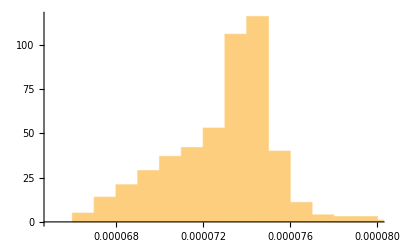

```mathematica
Table[Timing[ETensor[{μ,ν},{r1,s1}]][[1]],{n,500}];
Show[ListPlot[%,PlotMarkers->"x",AxesOrigin->{0,0},PlotRange->{{0,501},{0,1.2Max[%]}},PlotStyle->Black],Plot[{TrimmedMean[%,0.1],TrimmedMean[%,0.1]-StandardDeviation[%],TrimmedMean[%,0.1]+StandardDeviation[%]},{x,0,500},PlotStyle->{Black,Blue,Red},PlotLegends->{"TrimmedMean","TrimmedMean-StandardDeviation","TrimmedMean+StandardDeviation"}],ImageSize->Large]
Print["The trimmed mean evaluation time is "<>ToString[DecimalForm[TrimmedMean[%%,0.1]]]<>" seconds"]
Histogram[%%%]
```

-Graphics-

The trimmed mean evaluation time is 0.000234245 seconds

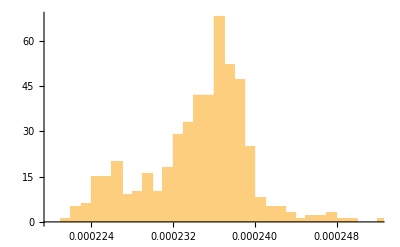

```mathematica
Table[Timing[ETensor[{μ,ν},{r1,s1,r2,s2}]][[1]],{n,500}];
Show[ListPlot[%,PlotMarkers->"x",AxesOrigin->{0,0},PlotRange->{{0,501},{0,1.2Max[%]}},PlotStyle->Black],Plot[{TrimmedMean[%,0.1],TrimmedMean[%,0.1]-StandardDeviation[%],TrimmedMean[%,0.1]+StandardDeviation[%]},{x,0,500},PlotStyle->{Black,Blue,Red},PlotLegends->{"TrimmedMean","TrimmedMean-StandardDeviation","TrimmedMean+StandardDeviation"}],ImageSize->Large]
Print["The trimmed mean evaluation time is "<>ToString[DecimalForm[TrimmedMean[%%,0.1]]]<>" seconds"]
Histogram[%%%]
```

-Graphics-

The trimmed mean evaluation time is 0.00128204 seconds

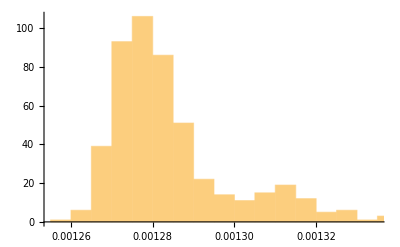

```mathematica
Table[Timing[ETensor[{μ,ν},{r1,s1,r2,s2,r3,s3}]][[1]],{n,500}];
Show[ListPlot[%,PlotMarkers->"x",AxesOrigin->{0,0},PlotRange->{{0,501},{0,1.2Max[%]}},PlotStyle->Black],Plot[{TrimmedMean[%,0.1],TrimmedMean[%,0.1]-StandardDeviation[%],TrimmedMean[%,0.1]+StandardDeviation[%]},{x,0,500},PlotStyle->{Black,Blue,Red},PlotLegends->{"TrimmedMean","TrimmedMean-StandardDeviation","TrimmedMean+StandardDeviation"}],ImageSize->Large]
Print["The trimmed mean evaluation time is "<>ToString[DecimalForm[TrimmedMean[%%,0.1]]]<>" seconds"]
Histogram[%%%]
```

-Graphics-

The trimmed mean evaluation time is 0.00613792 seconds

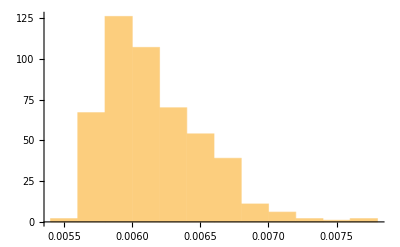

```mathematica
Table[Timing[ETensor[{μ,ν},{r1,s1,r2,s2,r3,s3,r4,s4}]][[1]],{n,500}];
Show[ListPlot[%,PlotMarkers->"x",AxesOrigin->{0,0},PlotRange->{{0,501},{0,1.2Max[%]}},PlotStyle->Black],Plot[{TrimmedMean[%,0.1],TrimmedMean[%,0.1]-StandardDeviation[%],TrimmedMean[%,0.1]+StandardDeviation[%]},{x,0,500},PlotStyle->{Black,Blue,Red},PlotLegends->{"TrimmedMean","TrimmedMean-StandardDeviation","TrimmedMean+StandardDeviation"}],ImageSize->Large]
Print["The trimmed mean evaluation time is "<>ToString[DecimalForm[TrimmedMean[%%,0.1]]]<>" seconds"]
Histogram[%%%]
```

-Graphics-

The trimmed mean evaluation time is 0.0664327 seconds

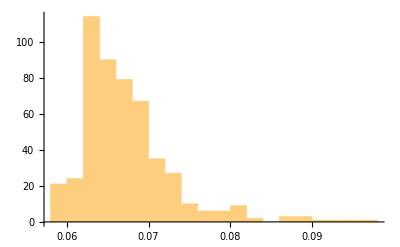

```mathematica
Table[Timing[ETensor[{μ,ν},{r1,s1,r2,s2,r3,s3,r4,s4,r5,s5}]][[1]],{n,500}];
Show[ListPlot[%,PlotMarkers->"x",AxesOrigin->{0,0},PlotRange->{{0,501},{0,1.2Max[%]}},PlotStyle->Black],Plot[{TrimmedMean[%,0.1],TrimmedMean[%,0.1]-StandardDeviation[%],TrimmedMean[%,0.1]+StandardDeviation[%]},{x,0,500},PlotStyle->{Black,Blue,Red},PlotLegends->{"TrimmedMean","TrimmedMean-StandardDeviation","TrimmedMean+StandardDeviation"}],ImageSize->Large]
Print["The trimmed mean evaluation time is "<>ToString[DecimalForm[TrimmedMean[%%,0.1]]]<>" seconds"]
Histogram[%%%]
```

-Graphics-

The trimmed mean evaluation time is 0.967978 seconds

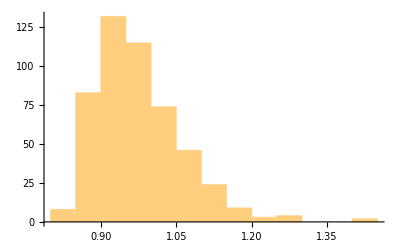

```mathematica
Table[Timing[ETensor[{μ,ν},{r1,s1,r2,s2,r3,s3,r4,s4,r5,s5,r6,s6}]][[1]],{n,500}];
Show[ListPlot[%,PlotMarkers->"x",AxesOrigin->{0,0},PlotRange->{{0,501},{0,1.2Max[%]}},PlotStyle->Black],Plot[{TrimmedMean[%,0.1],TrimmedMean[%,0.1]-StandardDeviation[%],TrimmedMean[%,0.1]+StandardDeviation[%]},{x,0,500},PlotStyle->{Black,Blue,Red},PlotLegends->{"TrimmedMean","TrimmedMean-StandardDeviation","TrimmedMean+StandardDeviation"}],ImageSize->Large]
Print["The trimmed mean evaluation time is "<>ToString[DecimalForm[TrimmedMean[%%,0.1]]]<>" seconds"]
Histogram[%%%]
```

# Scalar-graviton vertices

```mathematica
SetDirectory[NotebookDirectory[]];
SetDirectory["../Rules"];
<<GravitonScalarVertex`
```

FeynCalc 9.3.1 (stable version). For help, use the documentation center, check out the wiki or visit the forum.

To save your and our time, please check our FAQ for answers to some common FeynCalc questions.

See also the supplied examples. If you use FeynCalc in your research, please cite

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 256 (2020) 107478, arXiv:2001.04407.

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 207 (2016) 432-444, arXiv:1601.01167.

• R. Mertig, M. Böhm, and A. Denner, Comput. Phys. Commun. 64 (1991) 345-359.

## Kinetic term

-Graphics-

The trimmed mean evaluation time is 0.00504747 seconds

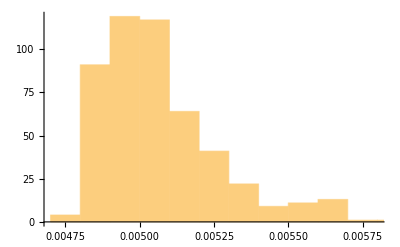

```mathematica
Table[Timing[GravitonScalarVertex[{μ1,ν1},p1,p2,m]][[1]],{n,500}];
Show[ListPlot[%,PlotMarkers->"x",AxesOrigin->{0,0},PlotRange->{{0,501},{0,1.2Max[%]}},PlotStyle->Black],Plot[{TrimmedMean[%,0.1],TrimmedMean[%,0.1]-StandardDeviation[%],TrimmedMean[%,0.1]+StandardDeviation[%]},{x,0,500},PlotStyle->{Black,Blue,Red},PlotLegends->{"TrimmedMean","TrimmedMean-StandardDeviation","TrimmedMean+StandardDeviation"}],ImageSize->Large]
Print["The trimmed mean evaluation time is "<>ToString[TrimmedMean[%%,0.1]]<>" seconds"]
Histogram[%%%]
```

-Graphics-

The trimmed mean evaluation time is 0.0221058 seconds

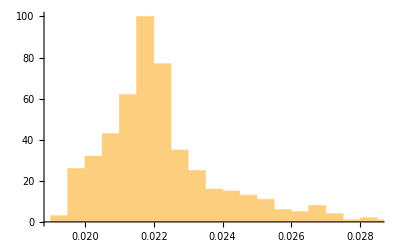

```mathematica
Table[Timing[GravitonScalarVertex[{μ1,ν1,μ2,ν2},p1,p2,m]][[1]],{n,500}];
Show[ListPlot[%,PlotMarkers->"x",AxesOrigin->{0,0},PlotRange->{{0,501},{0,1.2Max[%]}},PlotStyle->Black],Plot[{TrimmedMean[%,0.1],TrimmedMean[%,0.1]-StandardDeviation[%],TrimmedMean[%,0.1]+StandardDeviation[%]},{x,0,500},PlotStyle->{Black,Blue,Red},PlotLegends->{"TrimmedMean","TrimmedMean-StandardDeviation","TrimmedMean+StandardDeviation"}],ImageSize->Large]
Print["The trimmed mean evaluation time is "<>ToString[TrimmedMean[%%,0.1]]<>" seconds"]
Histogram[%%%]
```

-Graphics-

The trimmed mean evaluation time is 0.222296 seconds

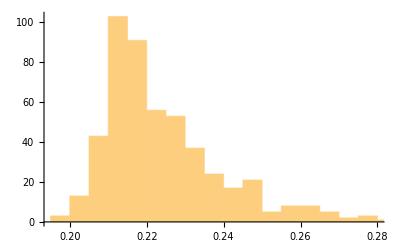

```mathematica
Table[Timing[GravitonScalarVertex[{μ1,ν1,μ2,ν2,μ3,ν3},p1,p2,m]][[1]],{n,500}];
Show[ListPlot[%,PlotMarkers->"x",AxesOrigin->{0,0},PlotRange->{{0,501},{0,1.2Max[%]}},PlotStyle->Black],Plot[{TrimmedMean[%,0.1],TrimmedMean[%,0.1]-StandardDeviation[%],TrimmedMean[%,0.1]+StandardDeviation[%]},{x,0,500},PlotStyle->{Black,Blue,Red},PlotLegends->{"TrimmedMean","TrimmedMean-StandardDeviation","TrimmedMean+StandardDeviation"}],ImageSize->Large]
Print["The trimmed mean evaluation time is "<>ToString[TrimmedMean[%%,0.1]]<>" seconds"]
Histogram[%%%]
```

-Graphics-

The trimmed mean evaluation time is 3.17652 seconds

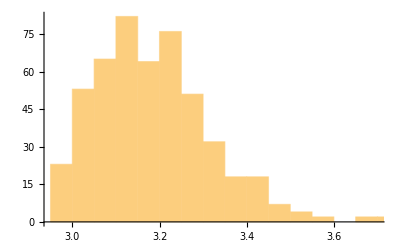

```mathematica
Table[Timing[GravitonScalarVertex[{μ1,ν1,μ2,ν2,μ3,ν3,μ4,ν4},p1,p2,m]][[1]],{n,500}];
Show[ListPlot[%,PlotMarkers->"x",AxesOrigin->{0,0},PlotRange->{{0,501},{0,1.2Max[%]}},PlotStyle->Black],Plot[{TrimmedMean[%,0.1],TrimmedMean[%,0.1]-StandardDeviation[%],TrimmedMean[%,0.1]+StandardDeviation[%]},{x,0,500},PlotStyle->{Black,Blue,Red},PlotLegends->{"TrimmedMean","TrimmedMean-StandardDeviation","TrimmedMean+StandardDeviation"}],ImageSize->Large]
Print["The trimmed mean evaluation time is "<>ToString[TrimmedMean[%%,0.1]]<>" seconds"]
Histogram[%%%]
```

-Graphics-

The trimmed mean evaluation time is 53.5205 seconds

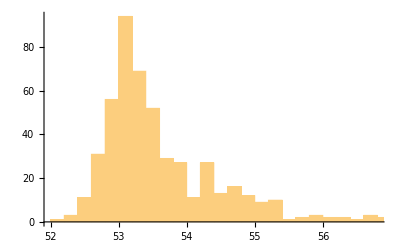

```mathematica
Table[Timing[GravitonScalarVertex[{μ1,ν1,μ2,ν2,μ3,ν3,μ4,ν4,μ5,ν5},p1,p2,m]][[1]],{n,500}];
Show[ListPlot[%,PlotMarkers->"x",AxesOrigin->{0,0},PlotRange->{{0,501},{0,1.2Max[%]}},PlotStyle->Black],Plot[{TrimmedMean[%,0.1],TrimmedMean[%,0.1]-StandardDeviation[%],TrimmedMean[%,0.1]+StandardDeviation[%]},{x,0,500},PlotStyle->{Black,Blue,Red},PlotLegends->{"TrimmedMean","TrimmedMean-StandardDeviation","TrimmedMean+StandardDeviation"}],ImageSize->Large]
Print["The trimmed mean evaluation time is "<>ToString[TrimmedMean[%%,0.1]]<>" seconds"]
Histogram[%%%]
```

## Potential term

-Graphics-

The trimmed mean evaluation time is 0.00032383 seconds

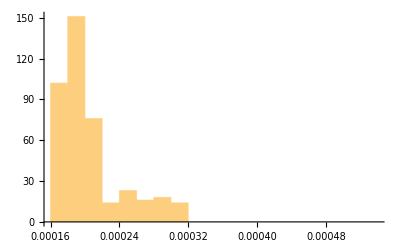

```mathematica
Table[Timing[GravitonScalarPotentialVertex[{μ1,ν1},λ]][[1]],{n,500}];
Show[ListPlot[%,PlotMarkers->"x",AxesOrigin->{0,0},PlotRange->{{0,501},{0,1.2Max[%]}},PlotStyle->Black],Plot[{TrimmedMean[%,0.1],TrimmedMean[%,0.1]-StandardDeviation[%],TrimmedMean[%,0.1]+StandardDeviation[%]},{x,0,500},PlotStyle->{Black,Blue,Red},PlotLegends->{"TrimmedMean","TrimmedMean-StandardDeviation","TrimmedMean+StandardDeviation"}],ImageSize->Large]
Print["The trimmed mean evaluation time is "<>ToString[TrimmedMean[%%,0.1]]<>" seconds"]
Histogram[%%%]
```

-Graphics-

The trimmed mean evaluation time is 0.000638695 seconds

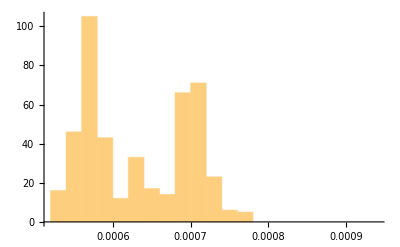

```mathematica
Table[Timing[GravitonScalarPotentialVertex[{μ1,ν1,μ2,ν2},λ]][[1]],{n,500}];
Show[ListPlot[%,PlotMarkers->"x",AxesOrigin->{0,0},PlotRange->{{0,501},{0,1.2Max[%]}},PlotStyle->Black],Plot[{TrimmedMean[%,0.1],TrimmedMean[%,0.1]-StandardDeviation[%],TrimmedMean[%,0.1]+StandardDeviation[%]},{x,0,500},PlotStyle->{Black,Blue,Red},PlotLegends->{"TrimmedMean","TrimmedMean-StandardDeviation","TrimmedMean+StandardDeviation"}],ImageSize->Large]
Print["The trimmed mean evaluation time is "<>ToString[TrimmedMean[%%,0.1]]<>" seconds"]
Histogram[%%%]
```

-Graphics-

The trimmed mean evaluation time is 0.00545836 seconds

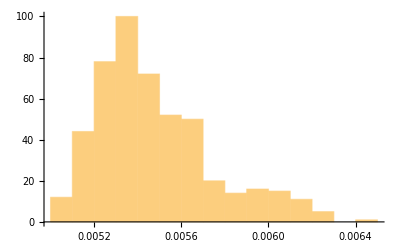

```mathematica
Table[Timing[GravitonScalarPotentialVertex[{μ1,ν1,μ2,ν2,μ3,ν3},λ]][[1]],{n,500}];
Show[ListPlot[%,PlotMarkers->"x",AxesOrigin->{0,0},PlotRange->{{0,501},{0,1.2Max[%]}},PlotStyle->Black],Plot[{TrimmedMean[%,0.1],TrimmedMean[%,0.1]-StandardDeviation[%],TrimmedMean[%,0.1]+StandardDeviation[%]},{x,0,500},PlotStyle->{Black,Blue,Red},PlotLegends->{"TrimmedMean","TrimmedMean-StandardDeviation","TrimmedMean+StandardDeviation"}],ImageSize->Large]
Print["The trimmed mean evaluation time is "<>ToString[TrimmedMean[%%,0.1]]<>" seconds"]
Histogram[%%%]
```

-Graphics-

The trimmed mean evaluation time is 0.0943187 seconds

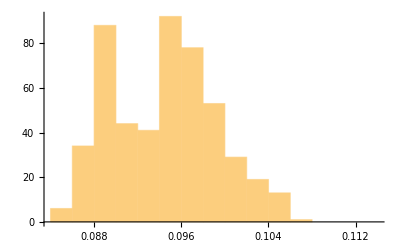

```mathematica
Table[Timing[GravitonScalarPotentialVertex[{μ1,ν1,μ2,ν2,μ3,ν3,μ4,ν4},λ]][[1]],{n,500}];
Show[ListPlot[%,PlotMarkers->"x",AxesOrigin->{0,0},PlotRange->{{0,501},{0,1.2Max[%]}},PlotStyle->Black],Plot[{TrimmedMean[%,0.1],TrimmedMean[%,0.1]-StandardDeviation[%],TrimmedMean[%,0.1]+StandardDeviation[%]},{x,0,500},PlotStyle->{Black,Blue,Red},PlotLegends->{"TrimmedMean","TrimmedMean-StandardDeviation","TrimmedMean+StandardDeviation"}],ImageSize->Large]
Print["The trimmed mean evaluation time is "<>ToString[TrimmedMean[%%,0.1]]<>" seconds"]
Histogram[%%%]
```

-Graphics-

The trimmed mean evaluation time is 2.09153 seconds

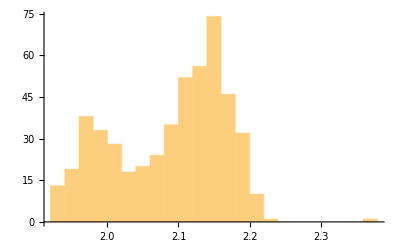

```mathematica
Table[Timing[GravitonScalarPotentialVertex[{μ1,ν1,μ2,ν2,μ3,ν3,μ4,ν4,μ5,ν5},λ]][[1]],{n,500}];
Show[ListPlot[%,PlotMarkers->"x",AxesOrigin->{0,0},PlotRange->{{0,501},{0,1.2Max[%]}},PlotStyle->Black],Plot[{TrimmedMean[%,0.1],TrimmedMean[%,0.1]-StandardDeviation[%],TrimmedMean[%,0.1]+StandardDeviation[%]},{x,0,500},PlotStyle->{Black,Blue,Red},PlotLegends->{"TrimmedMean","TrimmedMean-StandardDeviation","TrimmedMean+StandardDeviation"}],ImageSize->Large]
Print["The trimmed mean evaluation time is "<>ToString[TrimmedMean[%%,0.1]]<>" seconds"]
Histogram[%%%]
```

-Graphics-

The trimmed mean evaluation time is 58.7965 seconds

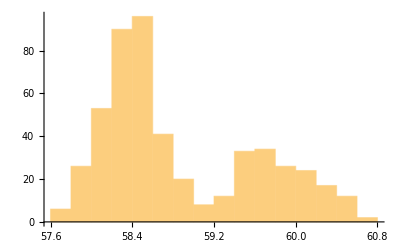

```mathematica
Table[Timing[GravitonScalarPotentialVertex[{μ1,ν1,μ2,ν2,μ3,ν3,μ4,ν4,μ5,ν5,μ6,ν6},λ]][[1]],{n,500}];
Show[ListPlot[%,PlotMarkers->"x",AxesOrigin->{0,0},PlotRange->{{0,501},{0,1.2Max[%]}},PlotStyle->Black],Plot[{TrimmedMean[%,0.1],TrimmedMean[%,0.1]-StandardDeviation[%],TrimmedMean[%,0.1]+StandardDeviation[%]},{x,0,500},PlotStyle->{Black,Blue,Red},PlotLegends->{"TrimmedMean","TrimmedMean-StandardDeviation","TrimmedMean+StandardDeviation"}],ImageSize->Large]
Print["The trimmed mean evaluation time is "<>ToString[TrimmedMean[%%,0.1]]<>" seconds"]
Histogram[%%%]
```

# Graviton-fermion vertex

```mathematica
SetDirectory[NotebookDirectory[]];
SetDirectory["../Rules"];
<<GravitonFermionVertex`
```

FeynCalc 9.3.1 (stable version). For help, use the documentation center, check out the wiki or visit the forum.

To save your and our time, please check our FAQ for answers to some common FeynCalc questions.

See also the supplied examples. If you use FeynCalc in your research, please cite

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 256 (2020) 107478, arXiv:2001.04407.

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 207 (2016) 432-444, arXiv:1601.01167.

• R. Mertig, M. Böhm, and A. Denner, Comput. Phys. Commun. 64 (1991) 345-359.

-Graphics-

The trimmed mean evaluation time is 0.00383738 seconds

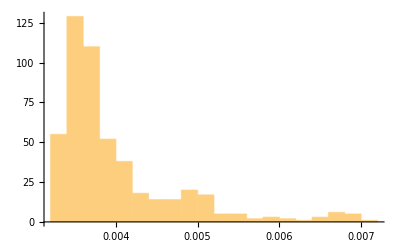

```mathematica
Table[Timing[GravitonFermionVertex[{r1,s1},p1,p2,m]][[1]],{n,500}];
Show[ListPlot[%,PlotMarkers->"x",AxesOrigin->{0,0},PlotRange->{{0,501},{0,1.2Max[%]}},PlotStyle->Black],Plot[{TrimmedMean[%,0.1],TrimmedMean[%,0.1]-StandardDeviation[%],TrimmedMean[%,0.1]+StandardDeviation[%]},{x,0,500},PlotStyle->{Black,Blue,Red},PlotLegends->{"TrimmedMean","TrimmedMean-StandardDeviation","TrimmedMean+StandardDeviation"}],ImageSize->Large]
Print["The trimmed mean evaluation time is "<>ToString[TrimmedMean[%%,0.1]]<>" seconds"]
Histogram[%%%]
```

-Graphics-

The trimmed mean evaluation time is 0.0205655 seconds

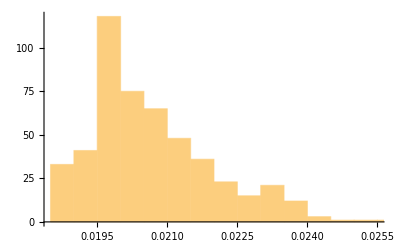

```mathematica
Table[Timing[GravitonFermionVertex[{r1,s1,r2,s2},p1,p2,m]][[1]],{n,500}];
Show[ListPlot[%,PlotMarkers->"x",AxesOrigin->{0,0},PlotRange->{{0,501},{0,1.2Max[%]}},PlotStyle->Black],Plot[{TrimmedMean[%,0.1],TrimmedMean[%,0.1]-StandardDeviation[%],TrimmedMean[%,0.1]+StandardDeviation[%]},{x,0,500},PlotStyle->{Black,Blue,Red},PlotLegends->{"TrimmedMean","TrimmedMean-StandardDeviation","TrimmedMean+StandardDeviation"}],ImageSize->Large]
Print["The trimmed mean evaluation time is "<>ToString[TrimmedMean[%%,0.1]]<>" seconds"]
Histogram[%%%]
```

-Graphics-

The trimmed mean evaluation time is 0.237939 seconds

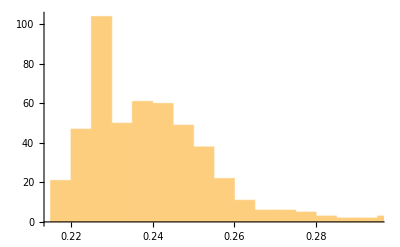

```mathematica
Table[Timing[GravitonFermionVertex[{r1,s1,r2,s2,r3,s3},p1,p2,m]][[1]],{n,500}];
Show[ListPlot[%,PlotMarkers->"x",AxesOrigin->{0,0},PlotRange->{{0,501},{0,1.2Max[%]}},PlotStyle->Black],Plot[{TrimmedMean[%,0.1],TrimmedMean[%,0.1]-StandardDeviation[%],TrimmedMean[%,0.1]+StandardDeviation[%]},{x,0,500},PlotStyle->{Black,Blue,Red},PlotLegends->{"TrimmedMean","TrimmedMean-StandardDeviation","TrimmedMean+StandardDeviation"}],ImageSize->Large]
Print["The trimmed mean evaluation time is "<>ToString[TrimmedMean[%%,0.1]]<>" seconds"]
Histogram[%%%]
```

-Graphics-

The trimmed mean evaluation time is 3.86312 seconds

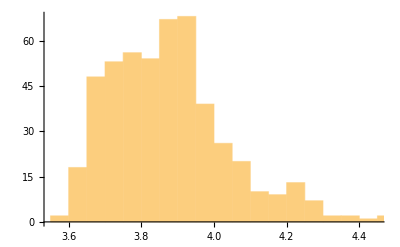

```mathematica
Table[Timing[GravitonFermionVertex[{r1,s1,r2,s2,r3,s3,r4,s4},p1,p2,m]][[1]],{n,500}];
Show[ListPlot[%,PlotMarkers->"x",AxesOrigin->{0,0},PlotRange->{{0,501},{0,1.2Max[%]}},PlotStyle->Black],Plot[{TrimmedMean[%,0.1],TrimmedMean[%,0.1]-StandardDeviation[%],TrimmedMean[%,0.1]+StandardDeviation[%]},{x,0,500},PlotStyle->{Black,Blue,Red},PlotLegends->{"TrimmedMean","TrimmedMean-StandardDeviation","TrimmedMean+StandardDeviation"}],ImageSize->Large]
Print["The trimmed mean evaluation time is "<>ToString[TrimmedMean[%%,0.1]]<>" seconds"]
Histogram[%%%]
```

# Graviton-vector vertices

```mathematica
SetDirectory[NotebookDirectory[]];
SetDirectory["../Rules"];
<<GravitonVectorVertex`
```

FeynCalc 9.3.1 (stable version). For help, use the documentation center, check out the wiki or visit the forum.

To save your and our time, please check our FAQ for answers to some common FeynCalc questions.

See also the supplied examples. If you use FeynCalc in your research, please cite

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 256 (2020) 107478, arXiv:2001.04407.

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 207 (2016) 432-444, arXiv:1601.01167.

• R. Mertig, M. Böhm, and A. Denner, Comput. Phys. Commun. 64 (1991) 345-359.

## Massive vectors

-Graphics-

The trimmed mean evaluation time is 0.0240353 seconds

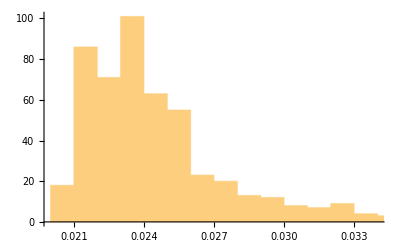

```mathematica
Table[Timing[GravitonMassiveVectorVertex[{μ1,ν1},λ1,p1,λ2,p2,m]][[1]],{n,500}];
Show[ListPlot[%,PlotMarkers->"x",AxesOrigin->{0,0},PlotRange->{{0,501},{0,1.2Max[%]}},PlotStyle->Black],Plot[{TrimmedMean[%,0.1],TrimmedMean[%,0.1]-StandardDeviation[%],TrimmedMean[%,0.1]+StandardDeviation[%]},{x,0,500},PlotStyle->{Black,Blue,Red},PlotLegends->{"TrimmedMean","TrimmedMean-StandardDeviation","TrimmedMean+StandardDeviation"}],ImageSize->Large]
Print["The trimmed mean evaluation time is "<>ToString[TrimmedMean[%%,0.1]]<>" seconds"]
Histogram[%%%]
```

```mathematica
Table[Timing[GravitonMassiveVectorVertex[{μ1,ν1,μ2,ν2},λ1,p1,λ2,p2,m]][[1]],{n,500}];
Show[ListPlot[%,PlotMarkers->"x",AxesOrigin->{0,0},PlotRange->{{0,501},{0,1.2Max[%]}},PlotStyle->Black],Plot[{TrimmedMean[%,0.1],TrimmedMean[%,0.1]-StandardDeviation[%],TrimmedMean[%,0.1]+StandardDeviation[%]},{x,0,500},PlotStyle->{Black,Blue,Red},PlotLegends->{"TrimmedMean","TrimmedMean-StandardDeviation","TrimmedMean+StandardDeviation"}],ImageSize->Large]
Print["The trimmed mean evaluation time is "<>ToString[TrimmedMean[%%,0.1]]<>" seconds"]
Histogram[%%%]
```

-Graphics-

The trimmed mean evaluation time is 0.164784 seconds

-Graphics-

```mathematica
Table[Timing[GravitonMassiveVectorVertex[{μ1,ν1,μ2,ν2,μ3,ν3},λ1,p1,λ2,p2,m]][[1]],{n,500}];
Show[ListPlot[%,PlotMarkers->"x",AxesOrigin->{0,0},PlotRange->{{0,501},{0,1.2Max[%]}},PlotStyle->Black],Plot[{TrimmedMean[%,0.1],TrimmedMean[%,0.1]-StandardDeviation[%],TrimmedMean[%,0.1]+StandardDeviation[%]},{x,0,500},PlotStyle->{Black,Blue,Red},PlotLegends->{"TrimmedMean","TrimmedMean-StandardDeviation","TrimmedMean+StandardDeviation"}],ImageSize->Large]
Print["The trimmed mean evaluation time is "<>ToString[TrimmedMean[%%,0.1]]<>" seconds"]
Histogram[%%%]
```

-Graphics-

The trimmed mean evaluation time is 1.96503 seconds

-Graphics-

```mathematica
Table[Timing[GravitonMassiveVectorVertex[{μ1,ν1,μ2,ν2,μ3,ν3,μ4,ν4},λ1,p1,λ2,p2,m]][[1]],{n,500}];
Show[ListPlot[%,PlotMarkers->"x",AxesOrigin->{0,0},PlotRange->{{0,501},{0,1.2Max[%]}},PlotStyle->Black],Plot[{TrimmedMean[%,0.1],TrimmedMean[%,0.1]-StandardDeviation[%],TrimmedMean[%,0.1]+StandardDeviation[%]},{x,0,500},PlotStyle->{Black,Blue,Red},PlotLegends->{"TrimmedMean","TrimmedMean-StandardDeviation","TrimmedMean+StandardDeviation"}],ImageSize->Large]
Print["The trimmed mean evaluation time is "<>ToString[TrimmedMean[%%,0.1]]<>" seconds"]
Histogram[%%%]
```

-Graphics-

The trimmed mean evaluation time is 36.682 seconds

-Graphics-

## Massless vectors

```mathematica
Table[Timing[GravitonVectorVertex[{μ1,ν1,k1},λ1,p1,λ2,p2,ε]][[1]],{n,500}];
Show[ListPlot[%,PlotMarkers->"x",AxesOrigin->{0,0},PlotRange->{{0,501},{0,1.2Max[%]}},PlotStyle->Black],Plot[{TrimmedMean[%,0.1],TrimmedMean[%,0.1]-StandardDeviation[%],TrimmedMean[%,0.1]+StandardDeviation[%]},{x,0,500},PlotStyle->{Black,Blue,Red},PlotLegends->{"TrimmedMean","TrimmedMean-StandardDeviation","TrimmedMean+StandardDeviation"}],ImageSize->Large]
Print["The trimmed mean evaluation time is "<>ToString[TrimmedMean[%%,0.1]]<>" seconds"]
Histogram[%%%]
```

-Graphics-

The trimmed mean evaluation time is 0.108053 seconds

-Graphics-

```mathematica
Table[Timing[GravitonVectorVertex[{μ1,ν1,k1,μ2,ν2,k2},λ1,p1,λ2,p2,ε]][[1]],{n,500}];
Show[ListPlot[%,PlotMarkers->"x",AxesOrigin->{0,0},PlotRange->{{0,501},{0,1.2Max[%]}},PlotStyle->Black],Plot[{TrimmedMean[%,0.1],TrimmedMean[%,0.1]-StandardDeviation[%],TrimmedMean[%,0.1]+StandardDeviation[%]},{x,0,500},PlotStyle->{Black,Blue,Red},PlotLegends->{"TrimmedMean","TrimmedMean-StandardDeviation","TrimmedMean+StandardDeviation"}],ImageSize->Large]
Print["The trimmed mean evaluation time is "<>ToString[TrimmedMean[%%,0.1]]<>" seconds"]
Histogram[%%%]
```

-Graphics-

The trimmed mean evaluation time is 1.68221 seconds

-Graphics-

```mathematica
Table[Timing[GravitonVectorVertex[{μ1,ν1,k1,μ2,ν2,k2,μ3,ν3,k3},λ1,p1,λ2,p2,ε]][[1]],{n,500}];
Show[ListPlot[%,PlotMarkers->"x",AxesOrigin->{0,0},PlotRange->{{0,501},{0,1.2Max[%]}},PlotStyle->Black],Plot[{TrimmedMean[%,0.1],TrimmedMean[%,0.1]-StandardDeviation[%],TrimmedMean[%,0.1]+StandardDeviation[%]},{x,0,500},PlotStyle->{Black,Blue,Red},PlotLegends->{"TrimmedMean","TrimmedMean-StandardDeviation","TrimmedMean+StandardDeviation"}],ImageSize->Large]
Print["The trimmed mean evaluation time is "<>ToString[TrimmedMean[%%,0.1]]<>" seconds"]
Histogram[%%%]
```

-Graphics-

The trimmed mean evaluation time is 40.6618 seconds

-Graphics-

## Ghosts

```mathematica
Table[Timing[GravitonVectorGhostVertex[{r1,s1},p1,p2]][[1]],{n,500}];
Show[ListPlot[%,PlotMarkers->"x",AxesOrigin->{0,0},PlotRange->{{0,501},{0,1.2Max[%]}},PlotStyle->Black],Plot[{TrimmedMean[%,0.1],TrimmedMean[%,0.1]-StandardDeviation[%],TrimmedMean[%,0.1]+StandardDeviation[%]},{x,0,500},PlotStyle->{Black,Blue,Red},PlotLegends->{"TrimmedMean","TrimmedMean-StandardDeviation","TrimmedMean+StandardDeviation"}],ImageSize->Large]
Print["The trimmed mean evaluation time is "<>ToString[TrimmedMean[%%,0.1]]<>" seconds"]
Histogram[%%%]
```

-Graphics-

The trimmed mean evaluation time is 0.00297293 seconds

-Graphics-

```mathematica
Table[Timing[GravitonVectorGhostVertex[{r1,s1,r2,s2},p1,p2]][[1]],{n,500}];
Show[ListPlot[%,PlotMarkers->"x",AxesOrigin->{0,0},PlotRange->{{0,501},{0,1.2Max[%]}},PlotStyle->Black],Plot[{TrimmedMean[%,0.1],TrimmedMean[%,0.1]-StandardDeviation[%],TrimmedMean[%,0.1]+StandardDeviation[%]},{x,0,500},PlotStyle->{Black,Blue,Red},PlotLegends->{"TrimmedMean","TrimmedMean-StandardDeviation","TrimmedMean+StandardDeviation"}],ImageSize->Large]
Print["The trimmed mean evaluation time is "<>ToString[TrimmedMean[%%,0.1]]<>" seconds"]
Histogram[%%%]
```

-Graphics-

The trimmed mean evaluation time is 0.018347 seconds

-Graphics-

```mathematica
Table[Timing[GravitonVectorGhostVertex[{r1,s1,r2,s2,r3,s3},p1,p2]][[1]],{n,500}];
Show[ListPlot[%,PlotMarkers->"x",AxesOrigin->{0,0},PlotRange->{{0,501},{0,1.2Max[%]}},PlotStyle->Black],Plot[{TrimmedMean[%,0.1],TrimmedMean[%,0.1]-StandardDeviation[%],TrimmedMean[%,0.1]+StandardDeviation[%]},{x,0,500},PlotStyle->{Black,Blue,Red},PlotLegends->{"TrimmedMean","TrimmedMean-StandardDeviation","TrimmedMean+StandardDeviation"}],ImageSize->Large]
Print["The trimmed mean evaluation time is "<>ToString[TrimmedMean[%%,0.1]]<>" seconds"]
Histogram[%%%]
```

-Graphics-

The trimmed mean evaluation time is 0.215183 seconds

-Graphics-

```mathematica
Table[Timing[GravitonVectorGhostVertex[{r1,s1,r2,s2,r3,s3,r4,s4},p1,p2]][[1]],{n,500}];
Show[ListPlot[%,PlotMarkers->"x",AxesOrigin->{0,0},PlotRange->{{0,501},{0,1.2Max[%]}},PlotStyle->Black],Plot[{TrimmedMean[%,0.1],TrimmedMean[%,0.1]-StandardDeviation[%],TrimmedMean[%,0.1]+StandardDeviation[%]},{x,0,500},PlotStyle->{Black,Blue,Red},PlotLegends->{"TrimmedMean","TrimmedMean-StandardDeviation","TrimmedMean+StandardDeviation"}],ImageSize->Large]
Print["The trimmed mean evaluation time is "<>ToString[TrimmedMean[%%,0.1]]<>" seconds"]
Histogram[%%%]
```

-Graphics-

The trimmed mean evaluation time is 3.17006 seconds

-Graphics-

# Graviton vertices

```mathematica
SetDirectory[NotebookDirectory[]];
SetDirectory["../Rules"];
<<GravitonVertex`
```

FeynCalc 9.3.1 (stable version). For help, use the documentation center, check out the wiki or visit the forum.

To save your and our time, please check our FAQ for answers to some common FeynCalc questions.

See also the supplied examples. If you use FeynCalc in your research, please cite

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 256 (2020) 107478, arXiv:2001.04407.

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 207 (2016) 432-444, arXiv:1601.01167.

• R. Mertig, M. Böhm, and A. Denner, Comput. Phys. Commun. 64 (1991) 345-359.

## Graviton vectors

```mathematica
Table[Timing[GravitonVertex[{μ1,ν1,p1,μ2,ν2,p2,μ3,ν3,p3},ε]][[1]],{n,500}];
Show[ListPlot[%,PlotMarkers->"x",AxesOrigin->{0,0},PlotRange->{{0,501},{0,1.2Max[%]}},PlotStyle->Black],Plot[{TrimmedMean[%,0.1],TrimmedMean[%,0.1]-StandardDeviation[%],TrimmedMean[%,0.1]+StandardDeviation[%]},{x,0,500},PlotStyle->{Black,Blue,Red},PlotLegends->{"TrimmedMean","TrimmedMean-StandardDeviation","TrimmedMean+StandardDeviation"}],ImageSize->Large]
Print["The trimmed mean evaluation time is "<>ToString[TrimmedMean[%%,0.1]]<>" seconds"]
Histogram[%%%]
```

-Graphics-

The trimmed mean evaluation time is 5.13667 seconds

-Graphics-